Biodistribution Studies

This program is designed to perform calculations and produce graphs based on data from biodistribution studies.  Answer the following questions in the text boxes provided.  You only have to list the organs if you need to create a template Excel file.  If you have already filled out a template from this program, you can leave the last text box blank.  After you have filled the text boxes, click “OK.”

```mathematica
Grid[{{"How many mice (or other model organisms) did you collect data for?",InputField[Dynamic[numMice],Number]},{"What is the half-life of the injected compound (in minutes)?",InputField[Dynamic[halfLife],Number]},{"List the organs you collected data for separated by commas (ex. bone,brain,skin):",InputField[Dynamic[organsInput],String]}},ItemSize->Full]
SelectionMove[EvaluationNotebook[],Next,Cell,4]
```

How many mice (or other model organisms) did you collect data for? | 
What is the half-life of the injected compound (in minutes)? | 
List the organs you collected data for separated by commas (ex. bone,brain,skin): |

```mathematica
Button["OK",FrontEndExecute[FrontEndToken["EvaluateInitialization"]]]
```

OK

Click “Next” below.

```mathematica
col1={"INFORMATION ABOUT MODEL ORGANISM:","Mouse ID:","Weight (g):","Sex:","Biodistribution time point in hrs(ex.24):","INJECTION DATA (ALL TIMES IN MILITARY TIME, NO UNITS):","Date Injected:","Time Injected:","Injected Compound:","Data Sample Count Start:","Time Sample Count Start:","Time Standard Count Start:","CPMs Standard Counted:","Background CPMs:","Dilution Factor (if not diluted, enter 1):","uL Injected:","uL Standard Counted:","ORGAN DATA (ADD OR DELETE ORGANS AS NEEDED):",""};
repeat[m_,n_Integer?Positive]:=Sequence@@ConstantArray[m,n]; (*code adapted from m_goldberg's reply in StackExchange forum:
https://mathematica.stackexchange.com/questions/92728/generating-repeated-elements-in-a-list *)
organsList=Quiet[StringSplit[organsInput,","]];
column1=Flatten[Append[col1,organsList]];
template=Quiet[Transpose[{column1,{"","","","","","","month","hours","","month","hours","hours","","","","","","","Weight of Tube + Organ:",repeat["",Length[organsList]]},{"","","","","","","day","minutes","","day","minutes","minutes","","","","","","","Weight of Tube:",repeat["",Length[organsList]]},{"","","","","","","year","","","year","","","","","","","","","CPMs in Tissue:",repeat["",Length[organsList]]},{"","","","","","","","","","","","","","","","","","","Sample Number",repeat["",Length[organsList]]}}]];
miceList=Range[1,numMice];
allSheets=repeat[template,numMice];
Button["Next",SelectionEvaluate[SelectedNotebook[]]]
```

Next

Click the "Download Template" button to save the Excel file with the extension ".xlsx" to your computer.  Open the downloaded file.  Enter the required data for each sheet (there is one for each model organism).  See the example below for help. Remember to save your changes!  If you have already filled out the template, skip this step and upload your completed Excel file below using the “Upload File" button.

```mathematica
Button["Download template",Export[SystemDialogInput["FileSave"],{allSheets},"XLSX"],Method->"Queued"]
```

Download template

-Graphics-

After you have updated and saved the Excel file, you are ready to upload your data.  Click the "Upload File" button and select the completed Excel file.

```mathematica
Button["Upload File",file=SystemDialogInput["FileOpen"];
If[file≠"$Canceled",alldata=Import[file,"Data"];],Method->"Queued"] (*code was adapted from Vahagn Poghosyan's reply in the StackExchange forum:
https://mathematica.stackexchange.com/questions/19985/system-dialog-input-with-button *)
```

Upload File

Click the "Get Results!" button to generate graphs of the % Injection Dose per Tissue and the % Injection Dose per Organ. Click the “Save” button below each graph to save it as a PDF file.

```mathematica
Button["Get Results!",FrontEndExecute[FrontEndToken["EvaluateNotebook"]]]
```

Get Results!

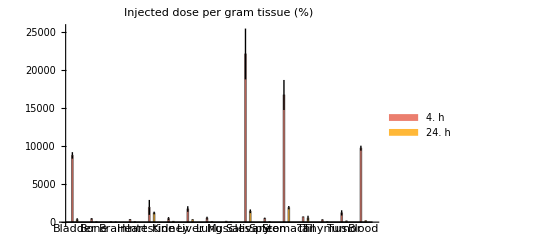

```mathematica
numMice=Length[alldata];
miceList=Range[1,numMice];
GetTimes=Function[{n},data=alldata[[n]];
data[[5,2]]];
times=Map[GetTimes,miceList];
pos=PositionIndex[times];
testGroups=Values[pos];
numGroups=Range[1,Length[testGroups]];
timeswUnits=Quantity[DeleteDuplicates[times],"hrs"];
CalcPercTissue=Function[n,data=alldata[[n]];
organs=DeleteCases[data[[20;;,1]],""];
TubeAndOrganWt=DeleteCases[data[[20;;,2]],""];
TubeWt=DeleteCases[data[[20;;,3]],""];
CPMsTissue=DeleteCases[data[[20;;,4]],""];
SampleNum=DeleteCases[data[[20;;,5]],""];
TissueWt=TubeAndOrganWt-TubeWt;
MouseWt=data[[3,2]];
BloodWt=MouseWt*0.057;
BrainWt=MouseWt*0.1;
MusclesWt=MouseWt*0.4;
SkinWt=MouseWt*0.19;
BoneWt=MouseWt*0.1;posBlood=Position[organs,"Blood"];
posBrain=Position[organs,"Brain"];
posMuscles=Position[organs,"Muscles"];
posSkin=Position[organs,"Skin"];
posBone=Position[organs,"Bone"];
OrganWt=ReplacePart[TissueWt,{posBlood->BloodWt,posBrain->BrainWt,posMuscles->MusclesWt,posSkin->SkinWt,posBone->BoneWt}];
TimeInjected=60*data[[8,2]]+data[[8,3]];
TimeSampleCountStart=24*60*Abs[(data[[10,3]]-data[[7,3]])]+60*data[[11,2]]+data[[11,3]];
TimeInjtoCountStart=TimeSampleCountStart-TimeInjected;
TissueSampleCounted=TimeSampleCountStart+(SampleNum-1);
ElapsedTimeFromInj=TimeInjtoCountStart+(SampleNum-1);
Bkgdcpms=data[[14,2]];
cpmsStdCounted=data[[13,2]];
StdBkgdCorrectedcpms=cpmsStdCounted-Bkgdcpms;
BkgdCorrectedCPM=CPMsTissue-Bkgdcpms;
DecayCorrectedCPM=BkgdCorrectedCPM/(Exp[(-0.693*ElapsedTimeFromInj)/halfLife]);
CPMgTissue=DecayCorrectedCPM/TissueWt;
DilutionFactor=data[[15,2]];
cpmsDilutionFactor=StdBkgdCorrectedcpms/DilutionFactor;
TimeStdCountStart=60*data[[12,2]]+data[[12,3]];
ElapsedTimePt=(TimeStdCountStart-TimeInjected);
StdDecayCorrectedcpms=cpmsDilutionFactor/Exp[(-0.693*ElapsedTimePt)/halfLife];
ulInjected=data[[16,2]];
ulStdCounted=data[[17,2]];
InjectedCPMs=StdDecayCorrectedcpms*ulInjected/ulStdCounted;
PercentInjDosegTissue=CPMgTissue/InjectedCPMs*100];
biodistFuncTissue=Function[u,group=testGroups[[u]];Map[CalcPercTissue,group]];
biodistTissue=Map[biodistFuncTissue,numGroups];
avgFuncTissue=Function[n,group=biodistTissue[[n]];average=Mean[group]];
avgTissue=Map[avgFuncTissue,numGroups];
repeatGroups=Function[m,Sequence@@ConstantArray[m,numOrgans]];
repeatOrgans=Function[m,Sequence@@ConstantArray[m,Length[numGroups]]];
numOrgans=Length[organs];
GroupNumList=Map[repeatGroups,numGroups];
OrganNumList=Flatten[{repeatOrgans[Range[numOrgans]]}];
errorFuncTissue=Function[{u,v},group=biodistTissue[[u]];col=group[[All,v]];
MeanAround[col]];
errorTissue=MapThread[errorFuncTissue,{GroupNumList,OrganNumList}];
chartData=Partition[errorTissue,numOrgans];
graphic=Show[BarChart[Transpose[chartData],ChartLabels->{organs,None},ChartLegends->timeswUnits,ChartStyle->24],PlotLabel->"Injected dose per gram tissue (%)",LabelStyle->Directive[Bold],ImageSize->Full]
```

```mathematica
Button["Save",Export[SystemDialogInput["FileSave"],graphic,"PDF"],Method->"Queued"]
```

Save

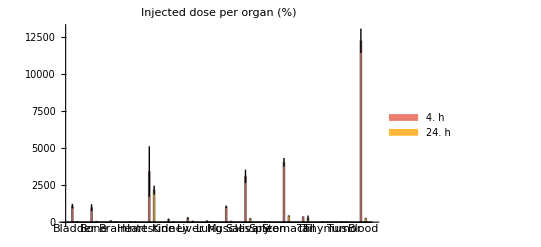

```mathematica
CalcPercOrgan=Function[n,data=alldata[[n]];
organs=DeleteCases[data[[20;;,1]],""];
TubeAndOrganWt=DeleteCases[data[[20;;,2]],""];
TubeWt=DeleteCases[data[[20;;,3]],""];
CPMsTissue=DeleteCases[data[[20;;,4]],""];
SampleNum=DeleteCases[data[[20;;,5]],""];
TissueWt=TubeAndOrganWt-TubeWt;
MouseWt=data[[3,2]];
BloodWt=MouseWt*0.057;
BrainWt=MouseWt*0.1;
MusclesWt=MouseWt*0.4;
SkinWt=MouseWt*0.19;
BoneWt=MouseWt*0.1;posBlood=Position[organs,"Blood"];
posBrain=Position[organs,"Brain"];
posMuscles=Position[organs,"Muscles"];
posSkin=Position[organs,"Skin"];
posBone=Position[organs,"Bone"];
OrganWt=ReplacePart[TissueWt,{posBlood->BloodWt,posBrain->BrainWt,posMuscles->MusclesWt,posSkin->SkinWt,posBone->BoneWt}];
TimeInjected=60*data[[8,2]]+data[[8,3]];
TimeSampleCountStart=24*60*Abs[(data[[10,3]]-data[[7,3]])]+60*data[[11,2]]+data[[11,3]];
TimeInjtoCountStart=TimeSampleCountStart-TimeInjected;
TissueSampleCounted=TimeSampleCountStart+(SampleNum-1);
ElapsedTimeFromInj=TimeInjtoCountStart+(SampleNum-1);
Bkgdcpms=data[[14,2]];
cpmsStdCounted=data[[13,2]];
StdBkgdCorrectedcpms=cpmsStdCounted-Bkgdcpms;
BkgdCorrectedCPM=CPMsTissue-Bkgdcpms;
DecayCorrectedCPM=BkgdCorrectedCPM/(Exp[(-0.693*ElapsedTimeFromInj)/halfLife]);
CPMgTissue=DecayCorrectedCPM/TissueWt;
DilutionFactor=data[[15,2]];
cpmsDilutionFactor=StdBkgdCorrectedcpms/DilutionFactor;
TimeStdCountStart=60*data[[12,2]]+data[[12,3]];
ElapsedTimePt=(TimeStdCountStart-TimeInjected);
StdDecayCorrectedcpms=cpmsDilutionFactor/Exp[(-0.693*ElapsedTimePt)/halfLife];
ulInjected=data[[16,2]];
ulStdCounted=data[[17,2]];
InjectedCPMs=StdDecayCorrectedcpms*ulInjected/ulStdCounted;
PercentInjDosegTissue=CPMgTissue/InjectedCPMs*100;cpmOrgan=CPMgTissue*OrganWt;PercentInjDoseOrgan=cpmOrgan/InjectedCPMs*100];
biodistFuncOrgan=Function[u,group=testGroups[[u]];Map[CalcPercOrgan,group]];
biodistOrgan=Map[biodistFuncOrgan,numGroups];
avgFuncOrgan=Function[m,group=biodistOrgan[[m]];average=Mean[group]];
avgOrgan=Map[avgFuncOrgan,numGroups];
errorFuncOrgan=Function[{u,v},group=biodistOrgan[[u]];col=group[[All,v]];
MeanAround[col]];
errorOrgan=MapThread[errorFuncOrgan,{GroupNumList,OrganNumList}];
chartData2=Partition[errorOrgan,numOrgans];
graphic2=Show[BarChart[Transpose[chartData2],ChartLabels->{organs,None},ChartLegends->timeswUnits,ChartStyle->24],PlotLabel->"Injected dose per organ (%)",LabelStyle->Directive[Bold],ImageSize->Full]
```

```mathematica
Button["Save",Export[SystemDialogInput["FileSave"],graphic2,"PDF"],Method->"Queued"]
```

Save

```mathematica
Module[{nb},nb=EvaluationNotebook[];
NotebookFind[EvaluationNotebook[],"Input",All,CellStyle];
SetOptions[NotebookSelection[nb],CellOpen->False,ShowCellBracket->True]] (*code adapted from David Reiss's response in Google group:
https://groups.google.com/g/comp.soft-sys.math.mathematica/c/OxD-QT-YsHw?pli=1 *)
```